```mathematica
projectDir = "/Users/pwrzosek/Documents/GitHub/AvoidedQP/t-J_model";
plotsDir ="./plots/";
dataDir="./data/";
SetDirectory[projectDir];
Off[ToExpression::sntx];
Off[ToExpression::sntxi];
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Definitions - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

(* Function for reading the Lehmann's representation of the Greens function from a file 'filename' *)
ReadData[filename_]:=(
stream = OpenRead[filename];
n = ToExpression[Read[stream, Word]];
momentum=Table[0.0,n];
energy=Table[{},n];
weight=Table[{},n];
doMomentum=True;
doEnergy=True;
doWeight=True;
in = 1;
While[in≤ n,(
If[doMomentum,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
momentum[[in]]=token;
doMomentum=False;
),
If[doEnergy,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
While[NumberQ[token],(
AppendTo[energy[[in]],token];
token=ToExpression[Read[stream, Word]];
)];
doEnergy=False;
),
If[doWeight,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
While[NumberQ[token],(
AppendTo[weight[[in]],token];
token=ToExpression[Read[stream, Word]];
)];
doWeight=False;
),(
doMomentum=True;
doEnergy=True;
doWeight=True;
in++;
)];
];
];
)];
Close[stream];
{momentum, energy, weight});

(* Returns exact representation of possible momenta in units of π *)
getMomentumInPi[momentum_]:= Round[momentum*(Length[momentum]-1)/(Pi)]/(Length[momentum]-1);

(* Calculates the spectral function A(k,ω) form Lehmann's representation of the Green's function *)
calculate[momentum_,energy_,weight_]:=(
ωMin=Min[energy];
ωMax=Max[energy];
iδ=0.05I;
ωSet=Table[ω, {ω,ωMin-1,ωMax,0.01}];
kSet=getMomentumInPi[momentum]*Pi;
A=Table[{kSet[[kDim]],ωSet[[ωDim]],-Im[Total[weight[[kDim]]/(ωSet[[ωDim]]+iδ-energy[[kDim]])]]/Pi},{ωDim,1,Length[ωSet]},{kDim,1,Length[kSet]}];
Flatten[A,1]);

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Definitions - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Listing Files - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

files=FileNames["lehmann_*.txt",dataDir];
TableForm[Transpose[{Table[n,{n,Length[files]}],files}]]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Listing Files - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

1 | ./data/lehmann_l=12_t=1.0_J=0.4_m=1.0_.txt
2 | ./data/lehmann_l=12_t=1.0_J=1.0_m=1.0_.txt
3 | ./data/lehmann_l=8_t=1.0_J=1.0_m=1.0_.txt

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Spectral Function - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

filename=files[[1]];
{momentum,energy,weight}=ReadData[filename];
A=calculate[momentum,energy,weight]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Spectral Function - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

{{0,-2.15115,0.000655225},{π/6,-2.15115,0.000857337},{π/3,-2.15115,0.00171168},{π/2,-2.15115,0.00328479},{(2 π)/3,-2.15115,0.0033273},{(5 π)/6,-2.15115,0.00249428},9751,{(7 π)/6,5.34885,0.000323556},{(4 π)/3,5.34885,0.000447439},{(3 π)/2,5.34885,0.000607238},{(5 π)/3,5.34885,0.000686808},{(11 π)/6,5.34885,0.000680756},{2 π,5.34885,0.000668195}}
 |  |  |  |

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Plot Setup - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

FrameTicksFontSize=18;
LegendFontSize=16;
colors="DeepSeaColors";
SetOptions[ListDensityPlot,InterpolationOrder->0,AspectRatio->1/2,ImageSize->600,ColorFunction->colors,FrameTicksStyle->Directive[FrameTicksFontSize,Black],FrameTicks-> {Automatic,{getMomentumInPi[momentum]*Pi,Automatic}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[LegendFontSize, Black]],Right]]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Plot Setup - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

{AlignmentPoint→Center,AspectRatio→1/2,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→DeepSeaColors,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→{Automatic,{{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π},Automatic}},FrameTicksStyle→Directive[18,GrayLevel[0]],GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→600,ImageSizeRaw→Automatic,InterpolationOrder→0,LabelStyle→{},LightingAngle→None,MaxPlotPoints→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→Placed[BarLegend[Automatic,LabelStyle→Directive[16,GrayLevel[0]]],Right],PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→Directive[16,GrayLevel[0]],VertexColors→Automatic}

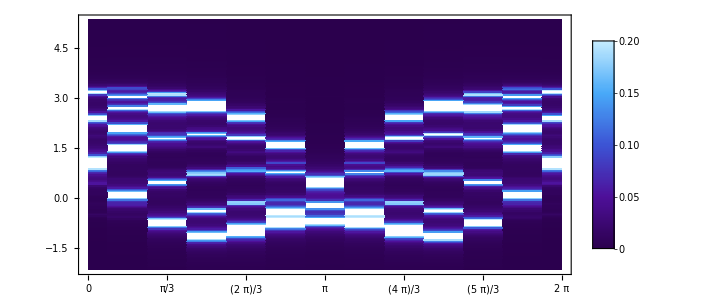

```mathematica
ListDensityPlot[A]
```

```mathematica
Max[energy]
```

5.3507966487310074655